4

5

7

8

15

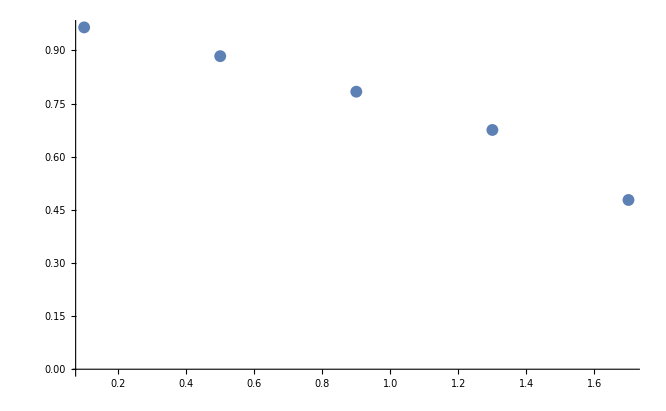

```mathematica
R0=1;
T0=1;
L=3;


(*Initial lattice config.*)

AngleBracket[a1_,a2_]:=Flatten[{a1[[1]]*a2[[1]]-a1[[2;;4]].a2[[2;;4]],a1[[1]]*a2[[2;;4]]+a2[[1]]*a1[[2;;4]]-Cross[a1[[2;;4]],a2[[2;;4]]]}];
Conj[a1_]:=Flatten[{a1[[1]],-a1[[2;;4]]}];

wilsonlink[β_]:=Module[ {F1,F2,act1,link1,list1,list2,r,u,g,f,J,ϵ,q},

F1=Table[{1,0,0,0},{i,L},{j,L},{k,L},{l,L},{m,L},{n,5}];
F2=Table[RandomPoint[Sphere[{0,0,0,0}]],{i,L},{j,L},{k,L},{l,L},{m,L},{n,5}];

(*Wilson Loop 1x1 Action *)
link1[F_,i_,j_,k_,l_,m_,d1_,d2_]:=Module[{del,delx},
del[n_,o_,p_,q_,r_]:=Part[F,Mod[i+n,L,1],Mod[j+o,L,1],Mod[k+p,L,1],Mod[l+q,L,1],Mod[m+r,L,1]];
delx[d_]:=del@@ReplacePart[{0,0,0,0,0},d->1];
Fold[⟨#1,#2⟩&,{del[0,0,0,0,0][[d1]],delx[d1][[d2]],delx[d2][[d1]]//Conj ,del[0,0,0,0,0][[d2]]//Conj}]
];

act1[F_]:=Module[{av},
av[i1_,j1_,k1_,l1_,m1_]:=link1[F,i1,j1,k1,l1,m1,#1,#2]&@@@Subsets[{1,2,3,4},{2}]//Total;

1-(Sum[av[i,j,k,l,m][[1]],{i,L},{j,L},{k,L},{l,L},{m,L}]/(6*(L^5)))
];



(*Energy Density Data*)

list1=List[act1[F1]];
list2=List[act1[F2]];

(*"Monte Carlo" Rejection Sampling*)

r[t_]:=Module[{o},While[True,o=RandomReal[{Exp[-t*β],Exp[t*β]}];
If[RandomReal[]<Sqrt[1-(Log[o]/(β*t))^2],Break[]];];
Return[Log[o]/(β*t)]
];

(*Neighbouring plaquettes*)

u[F_,i_,j_,k_,l_,m_,d_]:=Module[{del,delx,delx2,loop},

del[n_,o_,p_,q_,r_]:=Part[F,Mod[i+n,L,1],Mod[j+o,L,1],Mod[k+p,L,1],Mod[l+q,L,1],Mod[m+r,L,1]];
delx[v_,x_]:=del@@ReplacePart[{0,0,0,0,0},v->x];
delx2[v_,w_,x_,y_]:=del@@ReplacePart[{0,0,0,0,0},{v->x,w->y}];

loop[s_]:=Fold[⟨#1,#2⟩&,{delx[d,1][[s]],delx[s,1][[d]]//Conj ,del[0,0,0,0,0][[s]]//Conj}]+Fold[⟨#1,#2⟩&,{delx2[s,d,-1,1][[s]]//Conj,delx[s,-1][[d]]//Conj ,delx[s,-1][[s]]}];

loop/@Cases[{1,2,3,4,5},Except[d]]//Total

];


(*Generating Rule*)

g[F_,i_,j_,k_,l_,m_,d_]:=Module[{a0,a1,u0},
u0=u[F,i,j,k,l,m,d];
a0=r[Norm[u0]];
a1=RandomPoint[Sphere[{0,0,0},Sqrt[(1-a0^2)]]];
⟨Flatten[{a0,a1}],(u0/Norm[u0])//Conj⟩

];

f[n_]:=Module[{s,i,j,k,l,m,d},
s=n;
For[i=1,i<L+1,i++,
For[j=1,j<L+1,j++,
For[k=1,k<L+1,k++,
For[l=1,l<L+1,l++,
For[m=1,m<L+1,m++,
For[d=1,d<5+1,d++,
s[[i,j,k,l,m,d]]=g[s,i,j,k,l,m,d];
];
];
];
];
];
];
s
];



(*Run Simulation max J Times*)
J=15;
ϵ=0.01;
For[q=1,q<J,q++,
F1=f[F1];
list1=Append[list1,act1[F1]];
F2=f[F2];
list2=Append[list2,act1[F2]];
If[Abs[(list1[[-1]]-list2[[-1]])/(list1[[-1]]+list2[[-1]])]<ϵ&&Abs[(list1[[-1]]-list1[[-2]])/(list1[[-1]]+list1[[-2]])]<ϵ&&Abs[(list2[[-1]]-list2[[-2]])/(list2[[-1]]+list2[[-2]])]<ϵ,Break[]]
];
(*Print[ListPlot[{list1,list2},Joined->True,Mesh->Full,PlotRange->All,DataRange->All,PlotLegends->{"Trivial","Random"}]];*)
Print[Length[list1]];
(list1[[-1]]+list2[[-1]])/2
];

range=2;

data=Table[{β,wilsonlink[β]},{β,0.1,range,0.4}];
ListPlot[data,PlotRange->All]
```

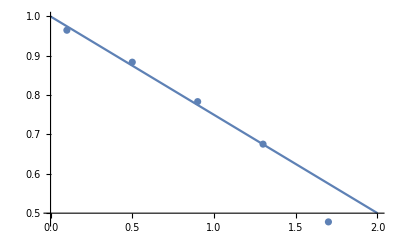

```mathematica
f[b_]:=1-(b/4);
(*g[b_]:=3/(4b);*)
Show[Plot[f[b],{b,0,range}],ListPlot[data,PlotRange->All],PlotRange->All]
```